0.03

0.11339

0.11339

{{v→InterpolatingFunction[{{0.,1500.}},<>],ncpa→InterpolatingFunction[{{0.,1500.}},<>]}}

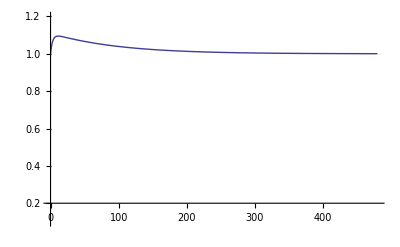

{{v→InterpolatingFunction[{{0.,1500.}},<>],ncpa→InterpolatingFunction[{{0.,1500.}},<>]}}

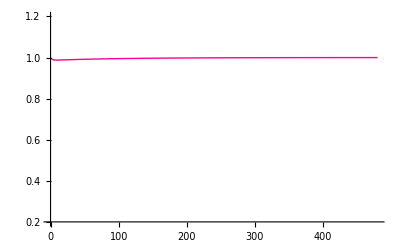

```mathematica
(* (c) 2012 by John Bischof.

This and other codes are provided under a limited 
academic license solely for the purpose of completing
 work in this class and any license for further 
use of the codes will be considered by the author 
upon written request.          *)


(* Cell diameter (meters) *)
d=100*(10^-6);

area = 3.14*10^4*(10^-6)^2;

(* Initial CPA molarity (moles/liter)   *)
moli=0;

(* Final CPA molarity (moles/liter)   *)
molf=2;

(* Ambient Temperature (degrees Kelvin) *)
temp=293;

(* Normalized osmotically inactive volume *)
(* of cell (unitless) *)
vb=.25;

(* Cell membrane hydraulic permeability  *)
(* cubic meters/Newton-sec  -   µm/min atm  *)
(* lp=1*(10^-13)  *)
lp=(10^-6)/(60*101000);
	
(* Cell membrane CPA permeability      *)
(* (moles/Newton-sec)  *)
Ps=0.03
(*m/s *)
P=Ps/6000;
(* conversion to cm/min *)
w = P/(8.314 (temp));

(*   w=50000*(10^-11);*)
	
(* Molar volume of CPA (cubic meters/mole) *)
vcpa=71.28*10^-6;
(* vcpa*10^3;  *)

(* Total time over which to perform  *)
(* calculations (seconds)  *)
totaltime=1000;

(* Other constants *)

(* Universal gas constant (calories/mole-K) *)
r=1.986;

(* Universal gas constant (Joules/mole-K) *)
r2=8.314;

(* Molar volume of water (cubic meters/mole)  *)
vw=18.8*10^-6;

(* Molar volume of salt (cubic meters/mole) *)
vs=27*10^-6;

(* Reflection coefficient in Kedem-Katchalsky *)
(* equations (unitless) *)

sig =1 - P*vcpa/(8.314 (temp)lp)
sig= 1 - w*vcpa/(lp)   

(* Same as 1 - PsVs/RTLp *)


moli=moli*1000;
(* moles / m^3 *)
molf=molf*1000;
vo=(4/3)*3.1415927*(d/2)^3;
vb=vb vo;
ns=300*(vo-vb);
cs2=300;
ncpai= moli*(vo-vb);
ncpao=molf*(vo-vb);
cc2=molf;
tr=273.15;

(* Functions *)
(* Weiss *)
cs1[v_]:=ns/(v-vb);
cc1[ncpa_,v_]:=ncpa/(v-vb);
jw[cs1_,cc1_]:=-lp r2 (temp) ((cs1-cs2)+sig (cc1-cc2));
jcpa[jw_,cs1_,cc1_]:=vcpa (((cc1+cc2)/2) (1-sig) jw+r2 (temp) w (cc1-cc2));
jv[jw_,jcpa_]:=jw+jcpa;
sol=NDSolve[
		{v'[t]==-area*
jv[jw[cs1[v[t]],cc1[ncpa[t],v[t]]],

jcpa[jw[cs1[v[t]],cc1[ncpa[t],v[t]]],cs1[v[t]],cc1[ncpa[t],v[t]]]] ,
			ncpa'[t]==-area 1/(vcpa 1)jcpa[jw[cs1[v[t]],cc1[ncpa[t],v[t]]],cs1[v[t]],cc1[ncpa[t],v[t]]] ,v[0]==vo,ncpa[0]==0},{v,ncpa},

{t,1500},MaxStepSize->.005,MaxSteps->300000]

pw2=Plot[Evaluate[{v[t]}/.sol]/vo,{t,0,480}, PlotRange->{.1,1.2}]

(* Kleinhans*)
cs1[v_]:=ns/(v-vb);
cc1[ncpa_,v_]:=ncpa/(v-vb);
jw[cs1_,cc1_]:=-lp r2 (temp) ((cs1-cs2)+(cc1-cc2));
jcpa[jw_,cs1_,cc1_]:=vcpa (r2 (temp) w (cc1-cc2));
jv[jw_,jcpa_]:=jw+jcpa;
sol=NDSolve[
		{v'[t]==-area*jv[jw[cs1[v[t]],cc1[ncpa[t],v[t]]],jcpa[jw[cs1[v[t]],cc1[ncpa[t],v[t]]],cs1[v[t]],cc1[ncpa[t],v[t]]]] ,
			ncpa'[t]==-area 1/vcpa jcpa[jw[cs1[v[t]],cc1[ncpa[t],v[t]]],cs1[v[t]],cc1[ncpa[t],v[t]]],v[0]==vo,ncpa[0]==0},{v,ncpa},{t,1500},MaxStepSize->.005,MaxSteps->300000]
p2p2=Plot[Evaluate[{v[t]}/.sol]/vo,{t,0,480}, PlotStyle->Hue[.9],PlotRange->{.2,1.2}]
```

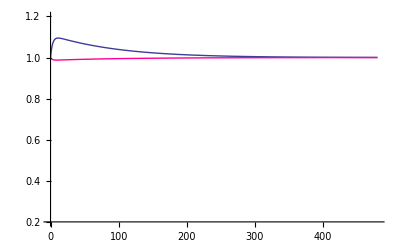

```mathematica
Show[pw2,p2p2,PlotRange->{.2,1.2}]
```